```mathematica
l=({{Subscript[λ, 11], Subscript[λ, 12], Subscript[λ, 13]}, {Subscript[λ, 21], Subscript[λ, 22], Subscript[λ, 23]}, {Subscript[λ, 31], Subscript[λ, 32], Subscript[λ, 33]}})
```

{{λ_11,λ_12,λ_13},{λ_21,λ_22,λ_23},{λ_31,λ_32,λ_33}}

```mathematica
Inverse[l]
```

{{(-λ_23 λ_32+λ_22 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(λ_13 λ_32-λ_12 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(-λ_13 λ_22+λ_12 λ_23)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)},{(λ_23 λ_31-λ_21 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(-λ_13 λ_31+λ_11 λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(λ_13 λ_21-λ_11 λ_23)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)},{(-λ_22 λ_31+λ_21 λ_32)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(λ_12 λ_31-λ_11 λ_32)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33),(-λ_12 λ_21+λ_11 λ_22)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)}}

```mathematica
MatrixForm[l.Inverse[l]]
```

((λ_13 (-λ_22 λ_31+λ_21 λ_32))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_12 (λ_23 λ_31-λ_21 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_11 (-λ_23 λ_32+λ_22 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_13 (λ_12 λ_31-λ_11 λ_32))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_12 (-λ_13 λ_31+λ_11 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_11 (λ_13 λ_32-λ_12 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_13 (-λ_12 λ_21+λ_11 λ_22))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_12 (λ_13 λ_21-λ_11 λ_23))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_11 (-λ_13 λ_22+λ_12 λ_23))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)
(λ_23 (-λ_22 λ_31+λ_21 λ_32))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_22 (λ_23 λ_31-λ_21 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_21 (-λ_23 λ_32+λ_22 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | (λ_23 (λ_12 λ_31-λ_11 λ_32))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_22 (-λ_13 λ_31+λ_11 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_21 (λ_13 λ_32-λ_12 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | ((-λ_12 λ_21+λ_11 λ_22) λ_23)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_22 (λ_13 λ_21-λ_11 λ_23))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_21 (-λ_13 λ_22+λ_12 λ_23))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)
((-λ_22 λ_31+λ_21 λ_32) λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_32 (λ_23 λ_31-λ_21 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_31 (-λ_23 λ_32+λ_22 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | ((λ_12 λ_31-λ_11 λ_32) λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_32 (-λ_13 λ_31+λ_11 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+(λ_31 (λ_13 λ_32-λ_12 λ_33))/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33) | ((-λ_13 λ_22+λ_12 λ_23) λ_31)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+((λ_13 λ_21-λ_11 λ_23) λ_32)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33)+((-λ_12 λ_21+λ_11 λ_22) λ_33)/(-λ_13 λ_22 λ_31+λ_12 λ_23 λ_31+λ_13 λ_21 λ_32-λ_11 λ_23 λ_32-λ_12 λ_21 λ_33+λ_11 λ_22 λ_33))

```mathematica
l^-1
```

{{1/λ_11,1/λ_12,1/λ_13},{1/λ_21,1/λ_22,1/λ_23},{1/λ_31,1/λ_32,1/λ_33}}

```mathematica
Simplify[l.Inverse[l]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
a=({{9, 2, 3}, {4, 5, 6}, {7, 8, 1}});
```

```mathematica
Det[a]
```

-320

```mathematica
Inverse[a]
```

{{43/320,-11/160,3/320},{-19/160,3/80,21/160},{3/320,29/160,-37/320}}

```mathematica
a.Inverse[a]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
(*expanding a polynomial*)

Expand[(1+x)^3(x-2 y)]
```

x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y

```mathematica
Factor[x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y]
```

(1+x)^3 (x-2 y)

```mathematica
Plot3D[(1+x)^3 (x-2 y),{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
Collect[x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y,y,Simplify]
```

x (1+x)^3-2 (1+x)^3 y

```mathematica
Simplify[x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y]
```

(1+x)^3 (x-2 y)

```mathematica
Cancel[(x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y)/(1+x)]
```

x+2 x^2+x^3-2 y-4 x y-2 x^2 y

```mathematica
Factor[(x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y)/(1+x)]
```

(1+x)^2 (x-2 y)

```mathematica
Simplify[5 Cos[θ]^4 Sin[θ]-10 Cos[θ]^2 Sin[θ]^3+Sin[θ]^5]
Simplify[(3-4Cos[2θ]+Cos[4θ])/(4(1+Cos[2θ]))]
```

Sin[5 θ]

Sin[θ]^2 Tan[θ]^2

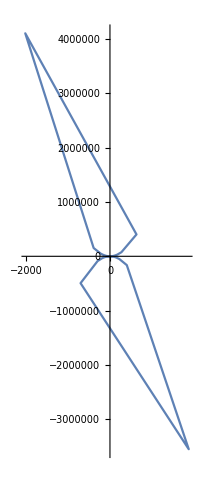

```mathematica
PolarPlot[Sin[θ]^2 Tan[θ]^2,{θ,0,2 π}]
```

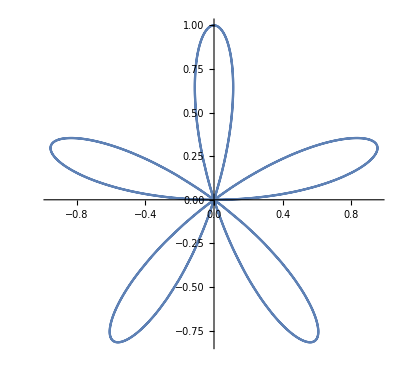

```mathematica
PolarPlot[Sin[5 θ],{θ,0,2 π}]
```

```mathematica
Simplify[(x^3 y^(4/3))/zw^5 √((x^3 w^5)/y)]
FullSimplify[(x^3 y^(4/3))/zw^5 √((x^3 w^5)/y)]
```

(x^3 √((w^5 x^3)/y) y^(4/3))/zw^5

(x^3 √((w^5 x^3)/y) y^(4/3))/zw^5

```mathematica
Simplify[√(x^2)]
Simplify[√(x^2),Assumptions->{x ∈Reals}]
PowerExpand[√(x^2)]
PowerExpand[√(p^2),Assumptions->{p∈ Reals}]
```

√(x^2)

Abs[x]

x

Abs[p]

```mathematica
PowerExpand[(x^3 y^(4/3))/zw^5 √((x^3 w^5)/y)]
```

(w^(5/2) x^(9/2) y^(5/6))/zw^5

```mathematica
poly = x+3 x^2+3 x^3+x^4-2 y-6 x y-6 x^2 y-2 x^3 y ;
poly/.x->2
```

54-54 y

```mathematica
poly /.{x->a+1,y->b-2}
```

1+a+3 (1+a)^2+3 (1+a)^3+(1+a)^4-2 (-2+b)-6 (1+a) (-2+b)-6 (1+a)^2 (-2+b)-2 (1+a)^3 (-2+b)

```mathematica
Factor[1+a+3 (1+a)^2+3 (1+a)^3+(1+a)^4-2 (-2+b)-6 (1+a) (-2+b)-6 (1+a)^2 (-2+b)-2 (1+a)^3 (-2+b)]
```

(2+a)^3 (5+a-2 b)

```mathematica
A=-829+1575y-1245 y^2+525 y^3-120 y^4+12 y^5;
Factor[A]
Simplify[A]
```

-829+1575 y-1245 y^2+525 y^3-120 y^4+12 y^5

-829+1575 y-1245 y^2+525 y^3-120 y^4+12 y^5

```mathematica
cList=CoefficientList[A,y]
FactorInteger[cList]
```

{-829,1575,-1245,525,-120,12}

{{{-1,1},{829,1}},{{3,2},{5,2},{7,1}},{{-1,1},{3,1},{5,1},{83,1}},{{3,1},{5,2},{7,1}},{{-1,1},{2,3},{3,1},{5,1}},{{2,2},{3,1}}}

```mathematica
FactorInteger[8]
```

{{2,3}}

```mathematica
B=Expand[A/.y->x+1]
CoefficientList[B,x]
FactorInteger[CoefficientList[B,x]]
```

-82+240 x-270 x^2+165 x^3-60 x^4+12 x^5

{-82,240,-270,165,-60,12}

{{{-1,1},{2,1},{41,1}},{{2,4},{3,1},{5,1}},{{-1,1},{2,1},{3,3},{5,1}},{{3,1},{5,1},{11,1}},{{-1,1},{2,2},{3,1},{5,1}},{{2,2},{3,1}}}

```mathematica
Table[B=Expand[A/.y->x+k],{k,-2,2}]
FactorInteger[CoefficientList[B,x]]
```

{-15463+17655 x-8235 x^2+1965 x^3-240 x^4+12 x^5,-4306+6180 x-3660 x^2+1125 x^3-180 x^4+12 x^5,-829+1575 x-1245 x^2+525 x^3-120 x^4+12 x^5,-82+240 x-270 x^2+165 x^3-60 x^4+12 x^5,5+15 x-15 x^2+45 x^3+12 x^5}

```mathematica
TableForm[
Table[Expand[A/.y->x+k],{k,-2,2}]
]
```

-15463+17655 x-8235 x^2+1965 x^3-240 x^4+12 x^5
-4306+6180 x-3660 x^2+1125 x^3-180 x^4+12 x^5
-829+1575 x-1245 x^2+525 x^3-120 x^4+12 x^5
-82+240 x-270 x^2+165 x^3-60 x^4+12 x^5
5+15 x-15 x^2+45 x^3+12 x^5

```mathematica
x+y/.{x->y,y->2}
x+y/.x->y/.y->2
```

2+y

4

```mathematica
(*Swapping of x and y*)
```

```mathematica
(x Sin[x y])/(√(x^2+y^3))/.{x->y,y->x}
(x Sin[x y])/(√(x^2+y^3))/.x->y/.y->x
```

(y Sin[x y])/(√(x^3+y^2))

(x Sin[x^2])/(√(x^2+x^3))

```mathematica
a b c/.x_ y_ ->x+y
```

a+b c

```mathematica
a b c //.x_ y_->x+y
```

a+b+c

```mathematica
a^2+bca-c/.x_  +y_+ z_ ->x  y z
```

-a^2 bca c

```mathematica
evens={0,2,4,6,8,10,12,14,16};
evens[[3]]
Part[evens,{4,6,-7}](* -7 was counted from the other side *)
```

4

{6,10,4}

```mathematica
Take[evens,3]
Take[evens,{2,-5}]
```

{0,2,4}

{2,4,6,8}

```mathematica
Drop[evens,{5,7}]
```

{0,2,4,6,14,16}

```mathematica
Simplify[√((w^3 x^-2 y^5)/(w^5 z^3))]
```

√(y^5/(w^2 x^2 z^3))

```mathematica
Simplify[-4 Sin[x]^3+4Cos[x] Sin[x]^2+3Sin[x]-Cos[x]]
```

-Cos[3 x]+Sin[3 x]

```mathematica
Table[
x^5-3 x^2+6/.x->x+k,{k,-4,4}
]
```

{6-3 (-4+x)^2+(-4+x)^5,6-3 (-3+x)^2+(-3+x)^5,6-3 (-2+x)^2+(-2+x)^5,6-3 (-1+x)^2+(-1+x)^5,6-3 x^2+x^5,6-3 (1+x)^2+(1+x)^5,6-3 (2+x)^2+(2+x)^5,6-3 (3+x)^2+(3+x)^5,6-3 (4+x)^2+(4+x)^5}

```mathematica
Table[
Coefficient[(x^2+x+1)^n,x^3],{n,2,25}
]
```

{2,7,16,30,50,77,112,156,210,275,352,442,546,665,800,952,1122,1311,1520,1750,2002,2277,2576,2900}

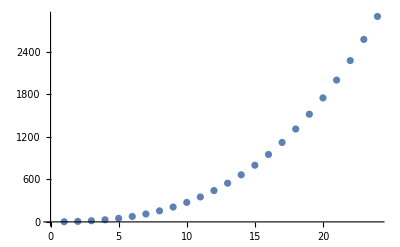

```mathematica
ListPlot[{2,7,16,30,50,77,112,156,210,275,352,442,546,665,800,952,1122,1311,1520,1750,2002,2277,2576,2900}]
```

```mathematica
TableForm[
Expand[
Table[
(x^2+x+1)^n,{n,2,25}
]
]
]
```

1+2 x+3 x^2+2 x^3+x^4
1+3 x+6 x^2+7 x^3+6 x^4+3 x^5+x^6
1+4 x+10 x^2+16 x^3+19 x^4+16 x^5+10 x^6+4 x^7+x^8
1+5 x+15 x^2+30 x^3+45 x^4+51 x^5+45 x^6+30 x^7+15 x^8+5 x^9+x^10
1+6 x+21 x^2+50 x^3+90 x^4+126 x^5+141 x^6+126 x^7+90 x^8+50 x^9+21 x^10+6 x^11+x^12
1+7 x+28 x^2+77 x^3+161 x^4+266 x^5+357 x^6+393 x^7+357 x^8+266 x^9+161 x^10+77 x^11+28 x^12+7 x^13+x^14
1+8 x+36 x^2+112 x^3+266 x^4+504 x^5+784 x^6+1016 x^7+1107 x^8+1016 x^9+784 x^10+504 x^11+266 x^12+112 x^13+36 x^14+8 x^15+x^16
1+9 x+45 x^2+156 x^3+414 x^4+882 x^5+1554 x^6+2304 x^7+2907 x^8+3139 x^9+2907 x^10+2304 x^11+1554 x^12+882 x^13+414 x^14+156 x^15+45 x^16+9 x^17+x^18
1+10 x+55 x^2+210 x^3+615 x^4+1452 x^5+2850 x^6+4740 x^7+6765 x^8+8350 x^9+8953 x^10+8350 x^11+6765 x^12+4740 x^13+2850 x^14+1452 x^15+615 x^16+210 x^17+55 x^18+10 x^19+x^20
1+11 x+66 x^2+275 x^3+880 x^4+2277 x^5+4917 x^6+9042 x^7+14355 x^8+19855 x^9+24068 x^10+25653 x^11+24068 x^12+19855 x^13+14355 x^14+9042 x^15+4917 x^16+2277 x^17+880 x^18+275 x^19+66 x^20+11 x^21+x^22
1+12 x+78 x^2+352 x^3+1221 x^4+3432 x^5+8074 x^6+16236 x^7+28314 x^8+43252 x^9+58278 x^10+69576 x^11+73789 x^12+69576 x^13+58278 x^14+43252 x^15+28314 x^16+16236 x^17+8074 x^18+3432 x^19+1221 x^20+352 x^21+78 x^22+12 x^23+x^24
1+13 x+91 x^2+442 x^3+1651 x^4+5005 x^5+12727 x^6+27742 x^7+52624 x^8+87802 x^9+129844 x^10+171106 x^11+201643 x^12+212941 x^13+201643 x^14+171106 x^15+129844 x^16+87802 x^17+52624 x^18+27742 x^19+12727 x^20+5005 x^21+1651 x^22+442 x^23+91 x^24+13 x^25+x^26
1+14 x+105 x^2+546 x^3+2184 x^4+7098 x^5+19383 x^6+45474 x^7+93093 x^8+168168 x^9+270270 x^10+388752 x^11+502593 x^12+585690 x^13+616227 x^14+585690 x^15+502593 x^16+388752 x^17+270270 x^18+168168 x^19+93093 x^20+45474 x^21+19383 x^22+7098 x^23+2184 x^24+546 x^25+105 x^26+14 x^27+x^28
1+15 x+120 x^2+665 x^3+2835 x^4+9828 x^5+28665 x^6+71955 x^7+157950 x^8+306735 x^9+531531 x^10+827190 x^11+1161615 x^12+1477035 x^13+1704510 x^14+1787607 x^15+1704510 x^16+1477035 x^17+1161615 x^18+827190 x^19+531531 x^20+306735 x^21+157950 x^22+71955 x^23+28665 x^24+9828 x^25+2835 x^26+665 x^27+120 x^28+15 x^29+x^30
1+16 x+136 x^2+800 x^3+3620 x^4+13328 x^5+41328 x^6+110448 x^7+258570 x^8+536640 x^9+996216 x^10+1665456 x^11+2520336 x^12+3465840 x^13+4343160 x^14+4969152 x^15+5196627 x^16+4969152 x^17+4343160 x^18+3465840 x^19+2520336 x^20+1665456 x^21+996216 x^22+536640 x^23+258570 x^24+110448 x^25+41328 x^26+13328 x^27+3620 x^28+800 x^29+136 x^30+16 x^31+x^32
1+17 x+153 x^2+952 x^3+4556 x^4+17748 x^5+58276 x^6+165104 x^7+410346 x^8+905658 x^9+1791426 x^10+3198312 x^11+5182008 x^12+7651632 x^13+10329336 x^14+12778152 x^15+14508939 x^16+15134931 x^17+14508939 x^18+12778152 x^19+10329336 x^20+7651632 x^21+5182008 x^22+3198312 x^23+1791426 x^24+905658 x^25+410346 x^26+165104 x^27+58276 x^28+17748 x^29+4556 x^30+952 x^31+153 x^32+17 x^33+x^34
1+18 x+171 x^2+1122 x^3+5661 x^4+23256 x^5+80580 x^6+241128 x^7+633726 x^8+1481108 x^9+3107430 x^10+5895396 x^11+10171746 x^12+16031952 x^13+23162976 x^14+30759120 x^15+37616427 x^16+42422022 x^17+44152809 x^18+42422022 x^19+37616427 x^20+30759120 x^21+23162976 x^22+16031952 x^23+10171746 x^24+5895396 x^25+3107430 x^26+1481108 x^27+633726 x^28+241128 x^29+80580 x^30+23256 x^31+5661 x^32+1122 x^33+171 x^34+18 x^35+x^36
1+19 x+190 x^2+1311 x^3+6954 x^4+30039 x^5+109497 x^6+344964 x^7+955434 x^8+2355962 x^9+5222264 x^10+10483934 x^11+19174572 x^12+32099094 x^13+49366674 x^14+69954048 x^15+91538523 x^16+110797569 x^17+124191258 x^18+128996853 x^19+124191258 x^20+110797569 x^21+91538523 x^22+69954048 x^23+49366674 x^24+32099094 x^25+19174572 x^26+10483934 x^27+5222264 x^28+2355962 x^29+955434 x^30+344964 x^31+109497 x^32+30039 x^33+6954 x^34+1311 x^35+190 x^36+19 x^37+x^38
1+20 x+210 x^2+1520 x^3+8455 x^4+38304 x^5+146490 x^6+484500 x^7+1409895 x^8+3656360 x^9+8533660 x^10+18062160 x^11+34880770 x^12+61757600 x^13+100640340 x^14+151419816 x^15+210859245 x^16+272290140 x^17+326527350 x^18+363985680 x^19+377379369 x^20+363985680 x^21+326527350 x^22+272290140 x^23+210859245 x^24+151419816 x^25+100640340 x^26+61757600 x^27+34880770 x^28+18062160 x^29+8533660 x^30+3656360 x^31+1409895 x^32+484500 x^33+146490 x^34+38304 x^35+8455 x^36+1520 x^37+210 x^38+20 x^39+x^40
1+21 x+231 x^2+1750 x^3+10185 x^4+48279 x^5+193249 x^6+669294 x^7+2040885 x^8+5550755 x^9+13599915 x^10+30252180 x^11+61476590 x^12+114700530 x^13+197278710 x^14+313817756 x^15+462919401 x^16+634569201 x^17+809676735 x^18+962803170 x^19+1067892399 x^20+1105350729 x^21+1067892399 x^22+962803170 x^23+809676735 x^24+634569201 x^25+462919401 x^26+313817756 x^27+197278710 x^28+114700530 x^29+61476590 x^30+30252180 x^31+13599915 x^32+5550755 x^33+2040885 x^34+669294 x^35+193249 x^36+48279 x^37+10185 x^38+1750 x^39+231 x^40+21 x^41+x^42
1+22 x+253 x^2+2002 x^3+12166 x^4+60214 x^5+251713 x^6+910822 x^7+2903428 x^8+8260934 x^9+21191555 x^10+49402850 x^11+105328685 x^12+206429300 x^13+373455830 x^14+625796996 x^15+974015867 x^16+1411306358 x^17+1907165337 x^18+2407049106 x^19+2840372304 x^20+3136046298 x^21+3241135527 x^22+3136046298 x^23+2840372304 x^24+2407049106 x^25+1907165337 x^26+1411306358 x^27+974015867 x^28+625796996 x^29+373455830 x^30+206429300 x^31+105328685 x^32+49402850 x^33+21191555 x^34+8260934 x^35+2903428 x^36+910822 x^37+251713 x^38+60214 x^39+12166 x^40+2002 x^41+253 x^42+22 x^43+x^44
1+23 x+276 x^2+2277 x^3+14421 x^4+74382 x^5+324093 x^6+1222749 x^7+4065963 x^8+12075184 x^9+32355917 x^10+78855339 x^11+175923090 x^12+361160835 x^13+685213815 x^14+1205682126 x^15+1973268693 x^16+3011119221 x^17+4292487562 x^18+5725520801 x^19+7154586747 x^20+8383467708 x^21+9217554129 x^22+9513228123 x^23+9217554129 x^24+8383467708 x^25+7154586747 x^26+5725520801 x^27+4292487562 x^28+3011119221 x^29+1973268693 x^30+1205682126 x^31+685213815 x^32+361160835 x^33+175923090 x^34+78855339 x^35+32355917 x^36+12075184 x^37+4065963 x^38+1222749 x^39+324093 x^40+74382 x^41+14421 x^42+2277 x^43+276 x^44+23 x^45+x^46
1+24 x+300 x^2+2576 x^3+16974 x^4+91080 x^5+412896 x^6+1621224 x^7+5612805 x^8+17363896 x^9+48497064 x^10+123286440 x^11+287134346 x^12+615939264 x^13+1222297740 x^14+2252056776 x^15+3864164634 x^16+6190070040 x^17+9276875476 x^18+13029127584 x^19+17172595110 x^20+21263575256 x^21+24755608584 x^22+27114249960 x^23+27948336381 x^24+27114249960 x^25+24755608584 x^26+21263575256 x^27+17172595110 x^28+13029127584 x^29+9276875476 x^30+6190070040 x^31+3864164634 x^32+2252056776 x^33+1222297740 x^34+615939264 x^35+287134346 x^36+123286440 x^37+48497064 x^38+17363896 x^39+5612805 x^40+1621224 x^41+412896 x^42+91080 x^43+16974 x^44+2576 x^45+300 x^46+24 x^47+x^48
1+25 x+325 x^2+2900 x^3+19850 x^4+110630 x^5+520950 x^6+2125200 x^7+7646925 x^8+24597925 x^9+71473765 x^10+189147400 x^11+458917850 x^12+1026360050 x^13+2125371350 x^14+4090293780 x^15+7338519150 x^16+12306291450 x^17+19331110150 x^18+28496073100 x^19+39478598170 x^20+51465297950 x^21+63191778950 x^22+73133433800 x^23+79818194925 x^24+82176836301 x^25+79818194925 x^26+73133433800 x^27+63191778950 x^28+51465297950 x^29+39478598170 x^30+28496073100 x^31+19331110150 x^32+12306291450 x^33+7338519150 x^34+4090293780 x^35+2125371350 x^36+1026360050 x^37+458917850 x^38+189147400 x^39+71473765 x^40+24597925 x^41+7646925 x^42+2125200 x^43+520950 x^44+110630 x^45+19850 x^46+2900 x^47+325 x^48+25 x^49+x^50

```mathematica
Log[x y]/.Log[a_ b_] ->Log[a]+Log[b]
Log[x/y]/.Log[a_/b_]->Log[a]-Log[b]
Log[(x y z)/w]//.Log[a_/b_]->Log[a]-Log[b]//.Log[a_ b_]->Log[a]+Log[b]
Log[(x y z)/w]//.{Log[a_ b_]->Log[a]+Log[b],Log[1/b_]->-Log[b]}
```

Log[x]+Log[y]

Log[x]-Log[y]

-Log[w]+Log[x]+Log[y]+Log[z]

-Log[w]+Log[x]+Log[y]+Log[z]

```mathematica
Simplify[Sum[i^3,{i,1,n}]]
```

1/4 n^2 (1+n)^2

```mathematica
TrigExpand[Sin[4x]]
```

4 Cos[x]^3 Sin[x]-4 Cos[x] Sin[x]^3

```mathematica
random = Sort[Table[RandomReal[],{i,1,20}]]
Take[random,{2,-2}]
random1=Table[RandomReal[20],{20}]
minPlaces1=Position[random1,Min[random1]]
temp1=Drop[random1,minPlaces1[[1]]]
maxPlaces1=Position[temp1,Max[temp1]]
Drop[temp1,maxPlaces1[[1]]]
```

{0.132836,0.147091,0.151129,0.206982,0.212922,0.238323,0.272555,0.446122,0.509824,0.51248,0.609126,0.667413,0.758728,0.774442,0.797357,0.888982,0.916712,0.920156,0.953979,0.973836}

{0.147091,0.151129,0.206982,0.212922,0.238323,0.272555,0.446122,0.509824,0.51248,0.609126,0.667413,0.758728,0.774442,0.797357,0.888982,0.916712,0.920156,0.953979}

{8.76517,13.8097,18.808,5.63371,7.68814,16.1234,3.84256,14.2439,0.685826,13.9813,5.77299,14.3697,16.2239,9.16695,0.836534,14.0216,15.9773,18.8849,13.3722,14.2596}

{{9}}

{8.76517,13.8097,18.808,5.63371,7.68814,16.1234,3.84256,14.2439,13.9813,5.77299,14.3697,16.2239,9.16695,0.836534,14.0216,15.9773,18.8849,13.3722,14.2596}

{{17}}

{8.76517,13.8097,18.808,5.63371,7.68814,16.1234,3.84256,14.2439,13.9813,5.77299,14.3697,16.2239,9.16695,0.836534,14.0216,15.9773,13.3722,14.2596}

```mathematica
data=Table[RandomInteger[5],{15}]
Min[data]
minPlaces=Position[data,Min[data]]
temp=Drop[data,minPlaces[[1]]]
minPlaces=Position[temp,Min[temp]]
Drop[temp,minPlaces[[1]]]
```

{1,3,3,1,2,4,0,1,2,3,0,3,1,2,5}

0

{{7},{11}}

{1,3,3,1,2,4,1,2,3,0,3,1,2,5}

{{10}}

{1,3,3,1,2,4,1,2,3,3,1,2,5}

```mathematica
ReplaceRepeated [x,a_-> 1+1/a ,MaxIterations->4]
```

1+1/(1+1/(1+1/(1+1/x)))

```mathematica
Product[Prime[i],{i,1,3}]
```

30

```mathematica
N[Product[(2k)^2/((2k-1)(2k+1)),{k,1,#}]]&/@{5,50,500}
N[π/2-Product[(2k)^2/((2k-1)(2k+1)),{k,1,#}]]&/@{5,50,1,500}
Product[(2k)^2/((2k-1)(2k+1)),{k,1,Infinity}]
```

{1.50109,1.56304,1.57001}

{0.0697083,0.00775688,0.237463,0.000784417}

π/2

```mathematica
data2=Table[RandomInteger[100],{10}]
data2/.{data2[[4]]->data2[[5]],data2[[5]]->data2[[4]]}
```

{73,12,84,94,66,40,71,47,33,99}

{73,12,84,66,94,40,71,47,33,99}